Todo :
Add extra parameters
 Add retroreflected beam (with shifted focus)
 Add Guoy phase
 Properly normalize the combined potential
 Fix Echo

# Calculation of lattice beam potential near the surface

Instructions : Run the whole notebook. Results are in the appropriate section.

## Parameter Setup

```mathematica
xFocusDisplacement = 3000;
yFocusDisplacement = 0;

zPeak = 24*0.532;
zUpper=zPeak-0.5*0.532;
zLower=zPeak+0.5*0.532;

latImbal=0;
```

## Calculation

General notes:
Distances are measured in micrometers. The positive z direction is pointing downwards, away from the substrate in calculations.

### Function definitions

```mathematica
gaussianE[x_, y_, z_, wx_, wy_]:= Module[{λ=1.064,k, zRayleighX, zRayleighY, localWaistX, localWaistY, invRCurvatureX, invRCurvatureY},
k= 2 π/λ;
zRayleighX= π wx^2/λ;
zRayleighY= π wy^2/λ;
localWaistX=wx Sqrt[1+(z/zRayleighX)^2];
localWaistY=wy Sqrt[1+(z/zRayleighY)^2];
invRCurvatureX=z/(z^2+zRayleighX^2);
invRCurvatureY=z/(z^2+zRayleighY^2);
Sqrt[(wx wy)/(localWaistX localWaistY)]Exp[-x^2/localWaistX^2 -y^2/localWaistY^2] Exp[-I k (z+x^2 invRCurvatureX/2 + y^2 invRCurvatureY/2)]]
```

```mathematica
reflectedBeamE[x_,y_, z_, θ_, wx_, wy_,focusDisplacement_] := Module[{xBeamIncoming=x Sin[θ] + z Cos[θ], zBeamIncoming=x Cos[θ]-z Sin[θ]-focusDisplacement, phaseShiftOutgoing = -1, xBeamOutgoing = -x Sin[θ]+z Cos[θ], zBeamOutgoing=x Cos[θ]+z Sin[θ]-focusDisplacement}, gaussianE[xBeamIncoming,y,  zBeamIncoming, wx, wy] + phaseShiftOutgoing*gaussianE[xBeamOutgoing,y, zBeamOutgoing, wx, wy]]
```

```mathematica
reflectedBeamI[x_,y_,  z_, θ_, wx_, wy_,focusDisplacement_] := Abs[reflectedBeamE[x,y, z, θ,wx, wy,focusDisplacement]]^2
```

### Calculations

Beams

```mathematica
xBeamPotential[x_, y_, z_] := reflectedBeamI[x,y,z,10.8 Degree,40,135,xFocusDisplacement]
yBeamPotential[x_, y_, z_] := reflectedBeamI[y,x,z,10.8 Degree,40,135,yFocusDisplacement]
xMaxFull = FindMaximum[xBeamPotential[xxMaxLoc,0,xzMaxLoc],{xxMaxLoc,0},{xzMaxLoc, 12.7685-0.005Exp[-xFocusDisplacement^2/6000^2]}];//Quiet
xMaxVal = xMaxFull[[1]];
xMaxRules=xMaxFull[[2]];
xxMaxLoc=xxMaxLoc/.xMaxRules;
xzMaxLoc=xzMaxLoc/.xMaxRules;
yMaxFull = FindMaximum[yBeamPotential[0,yyMaxLoc,yzMaxLoc],{yyMaxLoc,0},{yzMaxLoc, 12.7685-0.005Exp[-yFocusDisplacement^2/6000^2]}];//Quiet
yMaxVal = yMaxFull[[1]];
yMaxRules=yMaxFull[[2]];
yyMaxLoc=yyMaxLoc/.yMaxRules;
yzMaxLoc=yzMaxLoc/.yMaxRules;

xZMax[x_] := Quiet[Module[{z},z/. FindMaximum[xBeamPotential[x,0,z],{z, xzMaxLoc}][[2]]]];
yZMax[y_] := Quiet[Module[{z},z/. FindMaximum[xBeamPotential[0,y,z],{z, yzMaxLoc}][[2]]]];
```

Combined potential and gradient

```mathematica
totalPotentialWithZ[x_,y_,z_]:=(1+Max[0,latImbal])xBeamPotential[x+xxMaxLoc,y,z]/xMaxVal +(1+Max[0,-latImbal])yBeamPotential[x,y+yyMaxLoc,z]/yMaxVal;
totalPotentialHorizontal[x_,y_]:=totalPotentialWithZ[x,y,zPeak];
totalGradient[x_,y_]:=totalPotentialWithZ[x,y,zUpper]-totalPotentialWithZ[x,y,zLower];
```

### Intermediate results for debugging

```mathematica
Echo[{xMaxVal, xMaxRules}, "{Max potential depth of X lattice beam, Location of maximum}="];
Echo[{yMaxVal, yMaxRules}, "{Max potential depth of Y lattice beam, Location of maximum}="];
```

{Max potential depth of X lattice beam, Location of maximum}=  {2.93068,{1.81013→1.81013,12.7649→12.7649}}

{Max potential depth of Y lattice beam, Location of maximum}=  {3.28583,{0.→0.,12.7635→12.7635}}

## Results

Potential of the X Lattice beam along the beam and perpendicular to the substrate

```mathematica
DensityPlot[xBeamPotential[x,0, -z], {x, -20, 20}, {z, -15, 0}, PlotRange->Full, PlotPoints->100, Frame->True, FrameLabel->{"x [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

-Graphics-

Vertical position of X lattice beam power maximum along the beam centered at the beam maximum

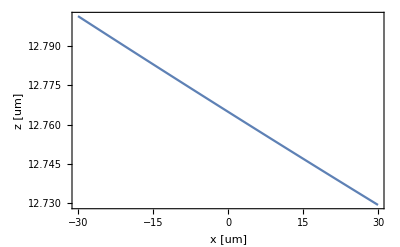

```mathematica
Plot[xZMax[(x+xxMaxLoc/.xMaxRules)], {x, -30, 30},PlotRange->Full, Frame->True, FrameLabel->{"x [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

Vertical position of Y lattice beam power maximum along the beam centered at the beam maximum

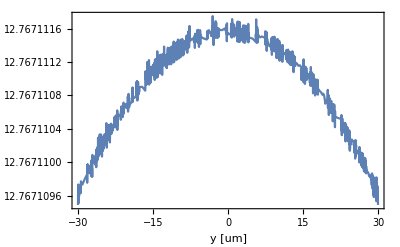

```mathematica
Plot[yZMax[(y+yyMaxLoc/.yMaxRules)], {y, -30, 30},PlotRange->Full, Frame->True, FrameLabel->{"y [um]", "z [um]"}, ImageSize->400, LabelStyle->20]
```

The lattice potential in red centered at the dimple location

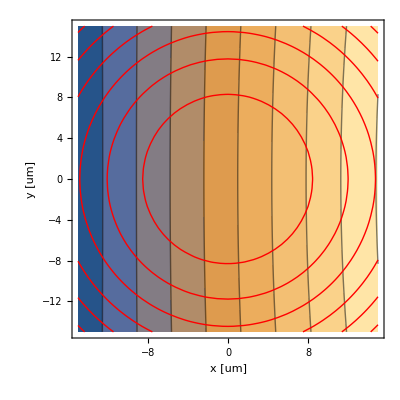

```mathematica
imgPotential=ContourPlot[totalPotentialHorizontal[x,y],{x, -15, 15}, {y, -15, 15}, PlotRange->Full,ContourShading->None, ContourStyle->Red, Frame->True, FrameLabel->{"x [um]", "y [um]"}, ImageSize->400, LabelStyle->20];
imgGradient=ContourPlot[totalGradient[x,y],{x, -15, 15}, {y, -15, 15}, PlotRange->Full, Frame->True, FrameLabel->{"x [um]", "y [um]"}, ImageSize->400, LabelStyle->20];
Show[{imgGradient,imgPotential}]
```